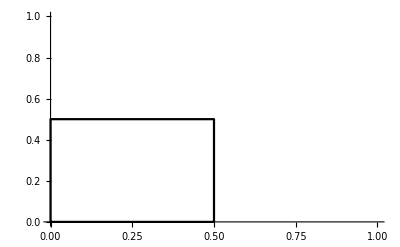

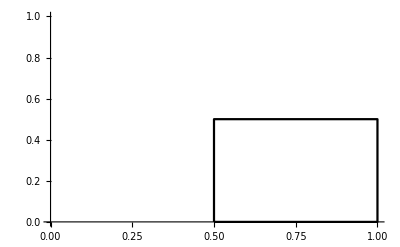

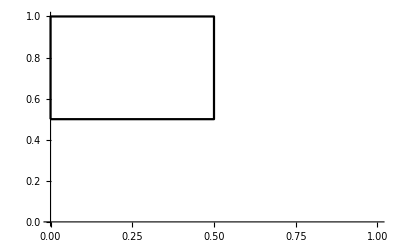

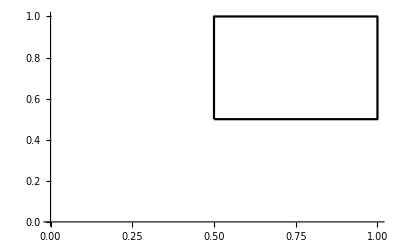

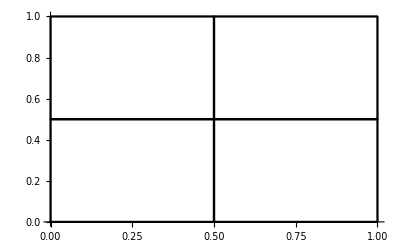

```mathematica
borderPoints = {{0, 0}, {0, 1}, {1, 1}, {1, 0}, {0, 0}};
ListLinePlot[borderPoints];

 leftBottom  = ListLinePlot[{{0, 0}, {0.5, 0}, {0.5, 0.5}, {0, 0.5}, {0, 0}}, PlotRange->{{0, 1}, {0, 1}}, PlotStyle->Black]
rightBottom  = ListLinePlot[{{0.5, 0}, {1, 0}, {1, 0.5}, {0.5, 0.5}, {0.5, 0}}, PlotRange->{{0, 1}, {0, 1}}, PlotStyle->Black]
leftTop  = ListLinePlot[{{0, 0.5}, {0.5, 0.5}, {0.5, 1}, {0, 1}, {0, 0.5}}, PlotRange->{{0, 1}, {0, 1}}, PlotStyle->Black]
rightTop  = ListLinePlot[{{0.5, 0.5}, {1, 0.5}, {1, 1}, {0.5, 1}, {0.5, 0.5}}, PlotRange->{{0, 1}, {0, 1}}, PlotStyle->Black]

allLines = Show[{leftBottom, rightBottom, leftTop, rightTop}]
```

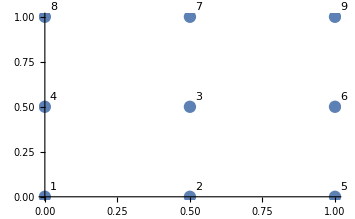

```mathematica
allPoints = {{0, 0,1}, {0.5, 0,2}, {0.5, 0.5, 3}, {0, 0.5, 4}, {1, 0, 5}, {1, 0.5, 6}, {0.5, 1, 7}, {0, 1, 8}, {1, 1, 9}};
allPointsPlot = ListPlot[Labeled[{#[[1]], #[[2]]},#[[3]]]&/@allPoints, PlotStyle -> PointSize[0.025]]
```

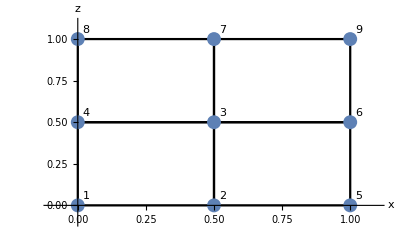

```mathematica
allPlot = Show[{leftBottom, rightBottom, leftTop, rightTop, allPointsPlot}, PlotRange->{{-0.1, 1.1}, {-0.1, 1.1}},AxesLabel->{"x","z"}]
```